```mathematica
Nt = 512; 
ti = 0; tf = 5; 
deltat = (tf - ti) /Nt ;
Nx = 128;
xi = -40; xf = 40; 
deltax = (xf - xi) / Nx; 
c =  1;

(*For Max Eigenvalue Plots*)
rs = Table[0.1*i,{i,1,200}];(*200 for Limits*)

maxevalsLD2 = Table[0,{i,1,Length[rs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsPI = Table[0,{i,1,Length[rs]}];



Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

selectwidth = 3;
diffOrder = 4;
deriv = 2;


(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);
(LP2=NDSolve`FiniteDifferenceDerivative[Derivative[4],grid,"DifferenceOrder"->diffOrder - 2]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);
LPX2 = LP2*((-1)^4)*(r*(Δx)^4);

gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;

gn2 = (LPX2[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX2 = Table[RotateRight[gn2,i],{i,-selectwidth,selectwidth}];
LPX2[[1,-1]]=0;
LPX2[[1,-2]]=0;
LPX2[[2,-1]]=0;
LPX2[[-1,1]]=0;
LPX2[[-1,2]]=0;
LPX2[[-2,1]]=0;
LPX2[[-3,1]] = 0;
LPX2[[-2,2]] = 0;
LPX2[[-1,3]] = 0;
LPX2[[1,-3]] = 0;
LPX2[[2,-2]] = 0;
LPX2[[3,-1]] = 0;


IP=IdentityMatrix[Length[LPX]];

(Mn=Inverse[IP-(ⅈ * LPX)/4  - LPX2/48 ].(IP+(ⅈ * LPX)/4- LPX2/48));

fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,1,Nx},{j,1,Nx}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - (n - 1)]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + (n - 1)]]  ,{n,1,selectwidth}],{i,1,Nx},{j,1,Nx}];*)
```

```mathematica
Do[
deltat = (deltax^2) * rs[[p]];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

f[x_] = ⅇ^(- x^2+ⅈ x);


(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp,"DifferenceOrder"->1, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL2 = L2[[2]] * deltat * (ⅈ / 2);


(* LD2 *)
ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];

evals = Eigenvalues[N[MLD2]];

maxevalsLD2[[p]] = Max[Abs[evals]];

(*PI*)
MPtest = N[MP//.{N[r -> deltat / (deltax)^2,32]},32];

evalsPI = Eigenvalues[N[MPtest]];

maxevalsPI[[p]] = Max[Abs[evalsPI]];

Print["Finished "<>ToString[rs[[p]]]];


,{p,1,Length[rs]}]


(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsLD2,maxevalsLD2,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];*)
(*Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

Finished 0.1

Finished 0.2

Finished 0.3

Finished 0.4

Finished 0.5

Finished 0.6

Finished 0.7

Finished 0.8

Finished 0.9

Finished 1.

Finished 1.1

Finished 1.2

Finished 1.3

Finished 1.4

Finished 1.5

Finished 1.6

Finished 1.7

Finished 1.8

Finished 1.9

Finished 2.

Finished 2.1

Finished 2.2

Finished 2.3

Finished 2.4

Finished 2.5

Finished 2.6

Finished 2.7

Finished 2.8

Finished 2.9

Finished 3.

Finished 3.1

Finished 3.2

Finished 3.3

Finished 3.4

Finished 3.5

Finished 3.6

Finished 3.7

Finished 3.8

Finished 3.9

Finished 4.

Finished 4.1

Finished 4.2

Finished 4.3

Finished 4.4

Finished 4.5

Finished 4.6

Finished 4.7

Finished 4.8

Finished 4.9

Finished 5.

Finished 5.1

Finished 5.2

Finished 5.3

Finished 5.4

Finished 5.5

Finished 5.6

Finished 5.7

Finished 5.8

Finished 5.9

Finished 6.

Finished 6.1

Finished 6.2

Finished 6.3

Finished 6.4

Finished 6.5

Finished 6.6

Finished 6.7

Finished 6.8

Finished 6.9

Finished 7.

Finished 7.1

Finished 7.2

Finished 7.3

Finished 7.4

Finished 7.5

Finished 7.6

Finished 7.7

Finished 7.8

Finished 7.9

Finished 8.

Finished 8.1

Finished 8.2

Finished 8.3

Finished 8.4

Finished 8.5

Finished 8.6

Finished 8.7

Finished 8.8

Finished 8.9

Finished 9.

Finished 9.1

Finished 9.2

Finished 9.3

Finished 9.4

Finished 9.5

Finished 9.6

Finished 9.7

Finished 9.8

Finished 9.9

Finished 10.

Finished 10.1

Finished 10.2

Finished 10.3

Finished 10.4

Finished 10.5

Finished 10.6

Finished 10.7

Finished 10.8

Finished 10.9

Finished 11.

Finished 11.1

Finished 11.2

Finished 11.3

Finished 11.4

Finished 11.5

Finished 11.6

Finished 11.7

Finished 11.8

Finished 11.9

Finished 12.

Finished 12.1

Finished 12.2

Finished 12.3

Finished 12.4

Finished 12.5

Finished 12.6

Finished 12.7

Finished 12.8

Finished 12.9

Finished 13.

Finished 13.1

Finished 13.2

Finished 13.3

Finished 13.4

Finished 13.5

Finished 13.6

Finished 13.7

Finished 13.8

Finished 13.9

Finished 14.

Finished 14.1

Finished 14.2

Finished 14.3

Finished 14.4

Finished 14.5

Finished 14.6

Finished 14.7

Finished 14.8

Finished 14.9

Finished 15.

Finished 15.1

Finished 15.2

Finished 15.3

Finished 15.4

Finished 15.5

Finished 15.6

Finished 15.7

Finished 15.8

Finished 15.9

Finished 16.

Finished 16.1

Finished 16.2

Finished 16.3

Finished 16.4

Finished 16.5

Finished 16.6

Finished 16.7

Finished 16.8

Finished 16.9

Finished 17.

Finished 17.1

Finished 17.2

Finished 17.3

Finished 17.4

Finished 17.5

Finished 17.6

Finished 17.7

Finished 17.8

Finished 17.9

Finished 18.

Finished 18.1

Finished 18.2

Finished 18.3

Finished 18.4

Finished 18.5

Finished 18.6

Finished 18.7

Finished 18.8

Finished 18.9

Finished 19.

Finished 19.1

Finished 19.2

Finished 19.3

Finished 19.4

Finished 19.5

Finished 19.6

Finished 19.7

Finished 19.8

Finished 19.9

Finished 20.

```mathematica
maxevalsLD2 = Join[{1},maxevalsLD2];
rsLD2 = Join[{0},rs];

maxevalsPI = Join[{1},maxevalsPI];
rsPI = Join[{0},rs];
```

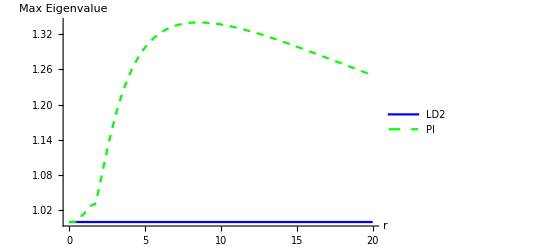

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"}, AxesLabel->{"r", "Max Eigenvalue"}]
```

```mathematica
(*ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"},PlotRange->{All,{.99,1.02}}, AxesLabel->{"r", "Max Eigenvalue"}]*)
```

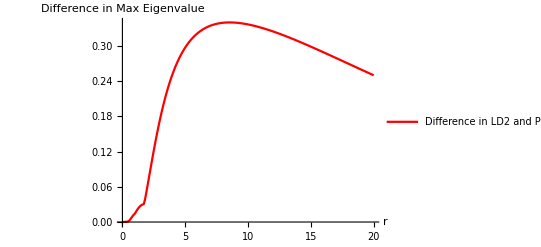

```mathematica
ListLinePlot[{Transpose[{rsLD2,Abs[maxevalsLD2 - maxevalsPI]}]},PlotStyle->{Red}, PlotLegends->{"Difference in LD2 and PI"}, AxesLabel->{"r", "Difference in Max Eigenvalue"}]
```

```mathematica
Abs[maxevalsLD2 - maxevalsPI]
```

{0,0.0000443694,0.000228756,0.000459421,0.000435082,0.00150296,0.00376748,0.00668873,0.0097416,0.0123756,0.0144091,0.0181447,0.0215305,0.0244323,0.0267796,0.0285502,0.0297599,0.0304543,0.038445,0.0499949,0.0619256,0.0740633,0.0862609,0.0983972,0.110374,0.122112,0.133553,0.14465,0.155371,0.165694,0.175604,0.185096,0.194166,0.20282,0.211062,0.218902,0.226351,0.233422,0.240127,0.246481,0.252498,0.258192,0.263578,0.26867,0.273481,0.278025,0.282315,0.286364,0.290182,0.293783,0.297176,0.300373,0.303383,0.306215,0.308878,0.311382,0.313733,0.315939,0.318009,0.319947,0.321761,0.323458,0.325041,0.326518,0.327893,0.32917,0.330355,0.331452,0.332465,0.333397,0.334253,0.335035,0.335748,0.336393,0.336975,0.337495,0.337957,0.338363,0.338715,0.339015,0.339267,0.339471,0.33963,0.339745,0.339818,0.339851,0.339846,0.339803,0.339725,0.339613,0.339468,0.339291,0.339083,0.338846,0.338581,0.338288,0.337969,0.337625,0.337256,0.336864,0.336449,0.336013,0.335555,0.335076,0.334578,0.334061,0.333525,0.332972,0.332402,0.331815,0.331212,0.330594,0.329961,0.329313,0.328651,0.327976,0.327288,0.326588,0.325875,0.32515,0.324415,0.323668,0.32291,0.322143,0.321365,0.320578,0.319782,0.318977,0.318164,0.317342,0.316512,0.315674,0.314829,0.313977,0.313118,0.312252,0.31138,0.310501,0.309617,0.308727,0.307831,0.30693,0.306024,0.305114,0.304198,0.303278,0.302354,0.301425,0.300493,0.299557,0.298617,0.297674,0.296728,0.295778,0.294826,0.29387,0.292912,0.291952,0.290989,0.290024,0.289057,0.288088,0.287117,0.286144,0.28517,0.284194,0.283217,0.282238,0.281259,0.280278,0.279296,0.278314,0.277331,0.276347,0.275363,0.274378,0.273393,0.272408,0.271423,0.270437,0.269452,0.268466,0.267481,0.266496,0.265512,0.264527,0.263544,0.26256,0.261578,0.260596,0.259615,0.258635,0.257655,0.256677,0.2557,0.254723,0.253748,0.252774,0.251801,0.25083,0.24986}

```mathematica
(*MP//MatrixForm*)
```

```mathematica
maxevalsPI
```

{1,1.00004,1.00023,1.00046,1.00044,1.0015,1.00377,1.00669,1.00974,1.01238,1.01441,1.01814,1.02153,1.02443,1.02678,1.02855,1.02976,1.03045,1.03844,1.04999,1.06193,1.07406,1.08626,1.0984,1.11037,1.12211,1.13355,1.14465,1.15537,1.16569,1.1756,1.1851,1.19417,1.20282,1.21106,1.2189,1.22635,1.23342,1.24013,1.24648,1.2525,1.25819,1.26358,1.26867,1.27348,1.27803,1.28232,1.28636,1.29018,1.29378,1.29718,1.30037,1.30338,1.30621,1.30888,1.31138,1.31373,1.31594,1.31801,1.31995,1.32176,1.32346,1.32504,1.32652,1.32789,1.32917,1.33036,1.33145,1.33246,1.3334,1.33425,1.33504,1.33575,1.33639,1.33697,1.3375,1.33796,1.33836,1.33871,1.33902,1.33927,1.33947,1.33963,1.33974,1.33982,1.33985,1.33985,1.3398,1.33973,1.33961,1.33947,1.33929,1.33908,1.33885,1.33858,1.33829,1.33797,1.33763,1.33726,1.33686,1.33645,1.33601,1.33555,1.33508,1.33458,1.33406,1.33353,1.33297,1.3324,1.33181,1.33121,1.33059,1.32996,1.32931,1.32865,1.32798,1.32729,1.32659,1.32587,1.32515,1.32441,1.32367,1.32291,1.32214,1.32137,1.32058,1.31978,1.31898,1.31816,1.31734,1.31651,1.31567,1.31483,1.31398,1.31312,1.31225,1.31138,1.3105,1.30962,1.30873,1.30783,1.30693,1.30602,1.30511,1.3042,1.30328,1.30235,1.30143,1.30049,1.29956,1.29862,1.29767,1.29673,1.29578,1.29483,1.29387,1.29291,1.29195,1.29099,1.29002,1.28906,1.28809,1.28712,1.28614,1.28517,1.28419,1.28322,1.28224,1.28126,1.28028,1.2793,1.27831,1.27733,1.27635,1.27536,1.27438,1.27339,1.27241,1.27142,1.27044,1.26945,1.26847,1.26748,1.2665,1.26551,1.26453,1.26354,1.26256,1.26158,1.2606,1.25961,1.25863,1.25766,1.25668,1.2557,1.25472,1.25375,1.25277,1.2518,1.25083,1.24986}